# Simple 1 D Ray Tracking

```mathematica
(* the ray is y = m x + c *)
(* the wires corrdinate on X1 plane is (X1, N) *)
```

## Generate Obervable (wire and drift-length)

```mathematica
(* RayPara = {m,c } *)
Ray[RayPara_,x_]:=RayPara[[1]] x+RayPara[[2]]
```

```mathematica
Xpos={-6,-2,2,6};
WirePos[planeX_,wireId_]:=Switch[planeX,
-6, wireId,
-2, wireId+0.25,
2,wireId,
6,wireId+0.25
]
Drift[planeX_,rayPara_]:=Module[{k},
k=Ray[rayPara,planeX];
Sort[
Table[
{wireId,Abs[k-WirePos[planeX,wireId]]+RandomReal[{-0.01,0.01}]}
,{wireId,Floor[k]-1,Ceiling[k]+1}
],#1[[2]]<#2[[2]]&][[1]]
]
Obser[rayPara_]:=Table[
Join[{Xpos[[i]]},Drift[Xpos[[i]],rayPara]]
,{i,1,Length[Xpos]}]
```

```mathematica
Drift[2,{0,0.9}]
Obser[{0,0.9}]
```

{1,0.0865725}

{{-5,1,0.142625},{-2,1,0.298054},{2,1,0.129705},{5,1,0.312305}}

## Ray Tracking

```mathematica
h[xList_]:=Table[{xList[[i]],1},{i,1,Length[xList]}]
Binery[n_,digit_]:=Module[{bin},
bin=Reverse[IntegerDigits[n,2]];
If[Length[bin]<digit,Join[bin,Table[0,{i,1,digit-Length[bin]}]], bin]
]
GenPossPos[obser_]:=Table[WirePos[obser[[j,1]],obser[[j,2]]]-Power[(-1),Binery[i,Length[obser]][[j]]]obser[[j,3]]
,{i,0,2^Length[obser]},{j,1,Length[obser]}]
RayTracking[obser_,Dis_]:=(
RayPos=GenPossPos[obser];
Xlist=Table[obser[[i,1]],{i,1,Length[obser]}];
H=h[Xlist];
SSError=Table[{i, LinearModelFit[{H,RayPos[[i]]}]["ANOVATableEntries"][[-2,2]]},{i,1, Length[RayPos]}];
SortedSSError= Sort[SSError,#1[[2]]<#2[[2]]&];
If[Dis,
TableForm[{
obser,
Table[Join[RayPos[[SortedSSError[[i,1]]]],SortedSSError[[i]]],{i,1,Length[RayPos]}]//TableForm,
"-----------------------",
TableForm[LinearModelFit[{H,RayPos[[SortedSSError[[1,1]]]]},{m,c}][{"ParameterConfidenceIntervalTable","ANOVATable"}]]}
,TableDepth->1],
Join[LinearModelFit[{H,RayPos[[SortedSSError[[1,1]]]]},{m,c}]["BestFitParameters"],
{LinearModelFit[{H,RayPos[[SortedSSError[[1,1]]]]},{m,c}]["ANOVATableEntries"][[-2,3]]}
]
])
GenPoints[rayPara_]:=Module[{pt},
pt=Obser[rayPara];
Join[
Table[{Xpos[[i]],WirePos[Xpos[[i]],pt[[i,2]]]+pt[[i,3]]},{i,1,Length[Xpos]}],
Table[{Xpos[[i]],WirePos[Xpos[[i]],pt[[i,2]]]-pt[[i,3]]},{i,1,Length[Xpos]}]
]
]
PlotFit[rayPara_]:=Module[{Fitdata},
Fitdata=RayTracking[Obser[rayPara],False][[1;;2]];
Plot[
{Ray[rayPara,x],Ray[Fitdata,x]},{x,Min[Xpos]-1,Max[Xpos]+1},
Epilog->{PointSize[Large],Point[GenPoints[rayPara]]},
GridLines->Automatic
]]
```

{-0.390851,0.945462}

-6 | 3 | 0.319068
-2 | 2 | 0.495321
2 | 0 | 0.133903
6 | -2 | 0.34859

{-0.387719,0.916442,0.000276834}

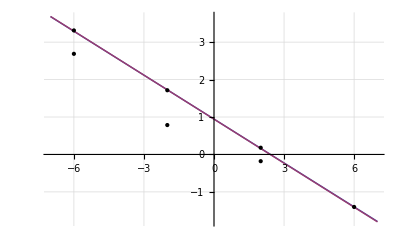

```mathematica
k={RandomReal[{-1,1}],RandomReal[{0,3}]}
Obser[k]//TableForm
RayTracking[Obser[k],False]
PlotFit[k]
```

## Ray Tracking From (All plane - 1)

```mathematica
planeID[obser_]:=Module[{size},
size = Length[obser];
Table[
If[Mod[i+j,size]==0, size,
Mod[i+j,size]],
{j,1,size},{i,1,size-1}]
]
ShinkObser[obser_]:=Module[{plane},
plane=planeID[obser];
Table[obser[[plane[[i]]]],{i,1,Length[plane]}]
]
RayTracking2[obser_,Dis_]:=Module[{data},
data=Join[{obser},ShinkObser[obser]];
Table[Join[{i-1},RayTracking[data[[i]],Dis]],{i,1,Length[data]}]
]
PlotFit2[rayPara_]:=Module[{Fitdata,pts},
Fitdata=RayTracking2[Obser[rayPara],False];
pts=GenPoints[rayPara];
Plot[
Evaluate[
Join[
{Ray[rayPara,x]},
Table[Ray[Fitdata[[i]][[2;;3]],x],{i,1,Length[Fitdata]}]
]
]
,{x,Min[Xpos]-1,Max[Xpos]+1},
Epilog->{PointSize[Large],Point[pts]},
GridLines->Automatic,
PlotRange->All,
PlotStyle->Table[Hue[(i-2)/Length[Fitdata]],{i,1,Length[Fitdata]}]
]
]
```

{0.81199,2.36089}

{{-6,-3,0.467689},{-2,0,0.463517},{2,4,0.00612021},{6,7,0.055152}}

0 | 0.820125 | 2.37312 | 0.00039452
1 | 0.823954 | 2.36035 | 6.88791×10^-6
2 | 0.819434 | 2.38003 | 0.000253999
3 | 0.810535 | 2.33237 | 7.61592×10^-6
4 | 0.815774 | 2.35658 | 0.00019877

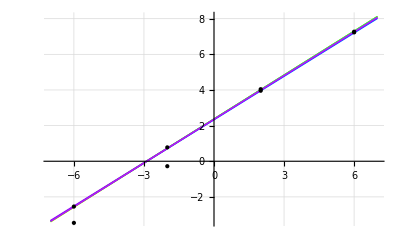

```mathematica
k={RandomReal[{-1,1}],RandomReal[{0,3}]}
data=Obser[k]
RayTracking2[data,False]//TableForm
PlotFit2[k]
```

## Statistics

```mathematica
kList=Table[{RandomReal[{-1,1}],RandomReal[{0,3}]},{i,1,500}];
TrackingList=Table[
RayTracking2[Obser[kList[[i]]],False]
,{i,1,500}];
```

```mathematica
M=h[Xpos];
ResponseList=Table[
M.TrackingList[[j,i,2;;3]]
,{j,1,500},{i,1,5}];
```

```mathematica
DiffAllList=Table[ResponseList[[j,1]]-Table[(Obser[kList[[j]]][[i,2]]),{i,1,4}],{j,1,500}];
Diff1List=Table[ResponseList[[j,2]]-Table[(Obser[kList[[j]]][[i,2]]),{i,1,4}],{j,1,500}];
Diff2List=Table[ResponseList[[j,3]]-Table[(Obser[kList[[j]]][[i,2]]),{i,1,4}],{j,1,500}];
Diff3List=Table[ResponseList[[j,4]]-Table[(Obser[kList[[j]]][[i,2]]),{i,1,4}],{j,1,500}];
Diff4List=Table[ResponseList[[j,5]]-Table[(Obser[kList[[j]]][[i,2]]),{i,1,4}],{j,1,500}];
```

```mathematica
Diff1Table=Table[{Diff1List[[i,1]],Obser[kList[[i]]][[1,3]]},{i,1,500}];
Diff2Table=Table[{Diff1List[[i,2]],Obser[kList[[i]]][[2,3]]},{i,1,500}];
Diff3Table=Table[{Diff1List[[i,3]],Obser[kList[[i]]][[3,3]]},{i,1,500}];
Diff4Table=Table[{Diff1List[[i,4]],Obser[kList[[i]]][[4,3]]},{i,1,500}];
```

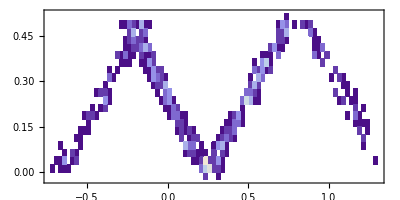

```mathematica
DensityHistogram[Diff4Table,{0.025},AspectRatio->0.5]
```

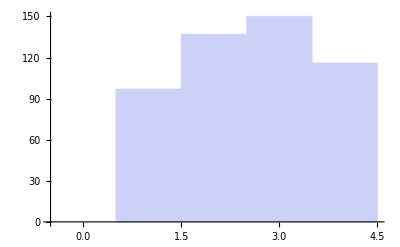

```mathematica
(* find the minium chisq of missing plane *)
MiniChi=Table[Sort[TrackingList[[i]],#1[[4]]<#2[[4]]&][[1,1]],{i,1,500}];
Histogram[MiniChi,{-0.5,4.5,1}]
```

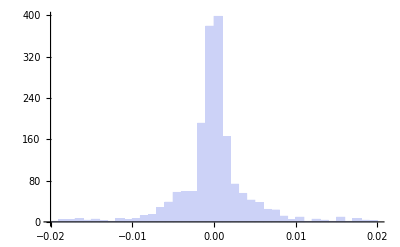

```mathematica
(* DIfference bewtwwn Ray3 and Ray4 *)
(* Difference of Slop *)
DiffSlop=Table[TrackingList[[j,1,2]]-TrackingList[[j,i,2]],{i,2,5},{j,1,500}];
Histogram[Flatten[DiffSlop],{-0.02,0.02,0.001}]
```

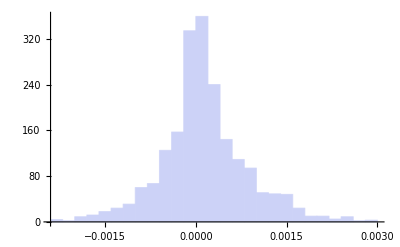

```mathematica
DiffChi=Table[TrackingList[[j,1,4]]-TrackingList[[j,i,4]],{i,2,5},{j,1,500}];
Histogram[Flatten[DiffChi]]
```

```mathematica
ChiPlaneAll=Table[TrackingList[[j,1,4]],{j,1,500}];
ChiPlane1=Table[TrackingList[[j,2,4]],{j,1,500}];
ChiPlane2=Table[TrackingList[[j,3,4]],{j,1,500}];
ChiPlane3=Table[TrackingList[[j,4,4]],{j,1,500}];
ChiPlane4=Table[TrackingList[[j,5,4]],{j,1,500}];
```

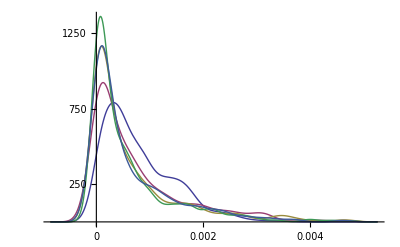

```mathematica
SmoothHistogram[{ChiPlaneAll,ChiPlane1,ChiPlane2,ChiPlane3,ChiPlane4}]
```